```mathematica
l={Cos[ϕ],Sin[ϕ]} t +{x,y}
```

{x+t Cos[ϕ],y+t Sin[ϕ]}

```mathematica
Solve[l.l==R^2,t]
```

{{t→(-2 x Cos[ϕ]-2 y Sin[ϕ]-√((2 x Cos[ϕ]+2 y Sin[ϕ])^2-4 (-R^2+x^2+y^2) (Cos[ϕ]^2+Sin[ϕ]^2)))/(2 (Cos[ϕ]^2+Sin[ϕ]^2))},{t→(-2 x Cos[ϕ]-2 y Sin[ϕ]+√((2 x Cos[ϕ]+2 y Sin[ϕ])^2-4 (-R^2+x^2+y^2) (Cos[ϕ]^2+Sin[ϕ]^2)))/(2 (Cos[ϕ]^2+Sin[ϕ]^2))}}

```mathematica
%//Simplify
```

{{t→-x Cos[ϕ]-y Sin[ϕ]-√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])},{t→-x Cos[ϕ]-y Sin[ϕ]+√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])}}

```mathematica
t/.%
```

{-x Cos[ϕ]-y Sin[ϕ]-√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ]),-x Cos[ϕ]-y Sin[ϕ]+√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])}

```mathematica
f[{x_,y_},ϕ_,R_]=%
```

{-x Cos[ϕ]-y Sin[ϕ]-√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ]),-x Cos[ϕ]-y Sin[ϕ]+√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])}

```mathematica
df[{x_,y_},ϕ_,R_,h_]=(f[{x,y},ϕ,R+h]-f[{x,y},ϕ,R])//Simplify
```

{√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])-√(((h+R)^2-y^2) Cos[ϕ]^2+((h+R)^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ]),-√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])+√(((h+R)^2-y^2) Cos[ϕ]^2+((h+R)^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])}

```mathematica
dp[{x_,y_},ϕ_,R_,h_,a_]=Times@@(1-Exp[- a Abs[df[{x,y},ϕ,R,h]]])//Expand
```

1-ⅇ^(-a Abs[√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])-√(((h+R)^2-y^2) Cos[ϕ]^2+((h+R)^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])])-ⅇ^(-a Abs[-√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])+√(((h+R)^2-y^2) Cos[ϕ]^2+((h+R)^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])])+ⅇ^(-a Abs[√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])-√(((h+R)^2-y^2) Cos[ϕ]^2+((h+R)^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])]-a Abs[-√((R^2-y^2) Cos[ϕ]^2+(R^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])+√(((h+R)^2-y^2) Cos[ϕ]^2+((h+R)^2-x^2) Sin[ϕ]^2+x y Sin[2 ϕ])])

```mathematica
dist=Table[{y,NIntegrate[dp[{0.0025,y},ϕ,0.450,0.02,10.],{ϕ,-Pi,Pi}]/(2 Pi)},{y,
0.00249,0.400,0.00249}]
```

{{0.00249,0.0328594},{0.00498,0.0328607},{0.00747,0.0328629},{0.00996,0.0328659},{0.01245,0.0328699},{0.01494,0.0328747},{0.01743,0.0328803},{0.01992,0.0328869},{0.02241,0.0328943},{0.0249,0.0329026},{0.02739,0.0329118},{0.02988,0.0329218},{0.03237,0.0329328},{0.03486,0.0329446},{0.03735,0.0329573},{0.03984,0.0329709},{0.04233,0.0329855},{0.04482,0.0330009},{0.04731,0.0330172},{0.0498,0.0330344},{0.05229,0.0330526},{0.05478,0.0330717},{0.05727,0.0330916},{0.05976,0.0331126},{0.06225,0.0331344},{0.06474,0.0331572},{0.06723,0.0331809},{0.06972,0.0332056},{0.07221,0.0332313},{0.0747,0.0332579},{0.07719,0.0332855},{0.07968,0.033314},{0.08217,0.0333436},{0.08466,0.0333741},{0.08715,0.0334056},{0.08964,0.0334382},{0.09213,0.0334718},{0.09462,0.0335063},{0.09711,0.033542},{0.0996,0.0335787},{0.10209,0.0336164},{0.10458,0.0336552},{0.10707,0.0336951},{0.10956,0.0337361},{0.11205,0.0337781},{0.11454,0.0338213},{0.11703,0.0338656},{0.11952,0.0339111},{0.12201,0.0339577},{0.1245,0.0340054},{0.12699,0.0340544},{0.12948,0.0341045},{0.13197,0.0341559},{0.13446,0.0342084},{0.13695,0.0342623},{0.13944,0.0343173},{0.14193,0.0343737},{0.14442,0.0344313},{0.14691,0.0344902},{0.1494,0.0345505},{0.15189,0.0346121},{0.15438,0.0346751},{0.15687,0.0347395},{0.15936,0.0348052},{0.16185,0.0348725},{0.16434,0.0349411},{0.16683,0.0350113},{0.16932,0.0350829},{0.17181,0.0351561},{0.1743,0.0352308},{0.17679,0.0353071},{0.17928,0.035385},{0.18177,0.0354645},{0.18426,0.0355457},{0.18675,0.0356286},{0.18924,0.0357132},{0.19173,0.0357996},{0.19422,0.0358877},{0.19671,0.0359777},{0.1992,0.0360696},{0.20169,0.0361633},{0.20418,0.036259},{0.20667,0.0363566},{0.20916,0.0364563},{0.21165,0.036558},{0.21414,0.0366619},{0.21663,0.0367678},{0.21912,0.036876},{0.22161,0.0369864},{0.2241,0.0370991},{0.22659,0.0372142},{0.22908,0.0373317},{0.23157,0.0374516},{0.23406,0.037574},{0.23655,0.037699},{0.23904,0.0378267},{0.24153,0.037957},{0.24402,0.0380902},{0.24651,0.0382261},{0.249,0.038365},{0.25149,0.0385069},{0.25398,0.0386519},{0.25647,0.0388},{0.25896,0.0389514},{0.26145,0.0391061},{0.26394,0.0392642},{0.26643,0.0394259},{0.26892,0.0395912},{0.27141,0.0397602},{0.2739,0.0399331},{0.27639,0.04011},{0.27888,0.0402909},{0.28137,0.0404761},{0.28386,0.0406656},{0.28635,0.0408596},{0.28884,0.0410582},{0.29133,0.0412617},{0.29382,0.0414701},{0.29631,0.0416836},{0.2988,0.0419024},{0.30129,0.0421268},{0.30378,0.0423568},{0.30627,0.0425927},{0.30876,0.0428348},{0.31125,0.0430832},{0.31374,0.0433382},{0.31623,0.0436},{0.31872,0.043869},{0.32121,0.0441455},{0.3237,0.0444296},{0.32619,0.0447218},{0.32868,0.0450225},{0.33117,0.0453319},{0.33366,0.0456505},{0.33615,0.0459786},{0.33864,0.0463168},{0.34113,0.0466655},{0.34362,0.0470253},{0.34611,0.0473966},{0.3486,0.04778},{0.35109,0.0481763},{0.35358,0.0485859},{0.35607,0.0490098},{0.35856,0.0494487},{0.36105,0.0499034},{0.36354,0.0503748},{0.36603,0.050864},{0.36852,0.051372},{0.37101,0.0519},{0.3735,0.0524494},{0.37599,0.0530214},{0.37848,0.0536178},{0.38097,0.0542402},{0.38346,0.0548905},{0.38595,0.0555707},{0.38844,0.0562833},{0.39093,0.0570308},{0.39342,0.0578161},{0.39591,0.0586425},{0.3984,0.0595137}}

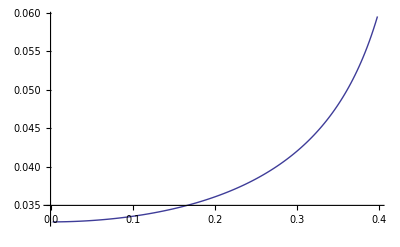

```mathematica
ListPlot[dist,PlotJoined->True]
```